# Precipitation Predictability at Extended Lead Times Over West Coast United States

BX Pan
2017.9.28

## Background

The Quiet Revolution of Numerical Weather Prediction

```mathematica
Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/RevolutionOfNWP.png"],1000],
	"Predictability(Correlation) of Extratropical 500hpa GPH from ECMWF,  Bauer, etc. Nature, 2015",Bottom]
```

-Graphics-Predictability(Correlation) of Extratropical 500hpa GPH from ECMWF,  Bauer, etc. Nature, 2015

Could “S2S forecasts be as widely used a decade from now as weather forecasts are today”?

The Ongoing Inquiry of the Foundation of “Climate Projection”

```mathematica
TableForm[{{"Initial Value Problem","Deterministic"},
           {"Boundary Value Problem","Proabilisitc"}},
          TableHeadings->{{"Weather Forecast","Climate Prediction"},None}]
```

Weather Forecast | Initial Value Problem | Deterministic
Climate Prediction | Boundary Value Problem | Proabilisitc

A deterministic system could be unpredictable:

Is the earth’s weather system ergodic? (more illustrations should be added here)

If it was ergodic, will an imperfect model be a valid predictor for the climate’s statistical features?

The Emerging Demand for Accurate and Extended Quantitative Precipitation Forecast(QPF)

```mathematica
Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/DemandForS2S.png"],1000],
	 "Demand For Accurate and Extended QPF, modified from the Earth System Prediction Capability Office.",Bottom]
```

-Graphics-Demand For Accurate and Extended QPF, modified from the Earth System Prediction Capability Office.

Predictability for extratropical and tropical areas are different, due to different precipitation mechanisms.

```mathematica
ImageResize[xkcdConvert[ListLinePlot[{{{1,0.86},{2,0.85},{3,0.75},{4,0.7},{5,0.65},{7,0.5},{10,0.3},{12,0.13},{14,0.13},{20,0.135},{30,0.2}},
              {{1,0.7},{2,0.65},{4,0.5},{7,0.45},{14,0.4},{20,0.42},{30,0.43}}},
              PlotStyle->{Blue,Red},
              Frame->True,
              Ticks->None,
              FrameLabel->{"Forecast Leading Days","Predictability"},
              Epilog -> 
   xkcdLabel /@ {{"Extratropic", {3, 0.75}, {1, 0}}, {"Tropic", {4, 0.5}, {0, -0.3}}}]],700]
```

-Graphics-

Extratropical predictability is mostly derived from synoptic-scale atmospheric dynamics

Tropical predictability is primarily derived from the response of moist convection to
slowly varying forcing such as from ENSO.

Subseasonal to Seasonal Prediction Project (2013-2018)

```mathematica
Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/dataset.jpg"],1000],
	 "The S2S Dataset",Bottom]
```

-Graphics- | Model | Ensemble Size | Extension(day) | Hincast Frequency
RGBColor[0, 1, 0] | BoM(Australia) | 33 | 62 | Every 5.1 days from 1981 to 2013
RGBColor[1, 0, 0] | CMA(China) | 4 | 60 | Every day from 1994 to 2014
RGBColor[0.5, 0, 0.5] | ECCC(Canada) | 4 | 32 | Every 4.1 days from 1995 to 2014
GrayLevel[0.5] | ECMWF(Europe) | 11 | 46 | Every 2.6 days from 1995 to 2016
RGBColor[1, 0, 1] | HMCR(Russia) | 10 | 61 | Every 2.9 days from 1985 to 2010
RGBColor[1, 1, 0] | ISAC-CNR(Italy) | 1 | 31 | Every 5. days from 1981 to 2010
RGBColor[0.94, 0.88, 0.94] | JMA(Japan) | 5 | 34 | Every 10.1 days from 1981 to 2010
RGBColor[0.6, 0.4, 0.2] | KMA(UnitedKingdom) | 3 | 60 | Every 10.9 days from 1991 to 2010
RGBColor[0, 1, 1] | Météo-France(France) | 15 | 61 | Every 15.2 days from 1993 to 2014
RGBColor[0, 0, 1] | NCEP(UnitedStates) | 4 | 44 | Every day from 1999 to 2010
RGBColor[1, 0.5, 0] | UKMO(UnitedKingdom) | 3 | 60 | Every 7.6 days from 1993 to 2015

## Opportunities and Challenges

Capacity to Predict MJO (average gain of 1 day of prediction skill per year)

Teleconnection between MJO and extratropics

North Atlantic Oscillation Index

2m temperature anormalies

Tropical Cyclones

Extratropical Storm Tracks

## Research Question

Where we are now in the respect of S2S predictability?

Dynamical Methods

Statistical Methods

## Literature Review

The most important aspect of the challenge is the chaotic nature of weather and climate predictability that needs to be characterized with probabilistic information.

## Data

S2S, sub-seasonal to seasonal prediction project, is a WWRP/THORPEX-WCRP joint research project established to improve forecast skill and understanding on the sub-seasonal to seasonal time scale, and promote its uptake by operational centres and exploitation by the applications community.

```mathematica
TableForm[{{"","Ocean Model","Sea Ice Model","Landsurface Model",""},
           {"BoM","ACOM2 (Schiller and Godfrey 2003)","",""},
           {"BoM","ACOM2 (Schiller and Godfrey 2003)","",""}}]
```

Initial conditions and perturbations

Data assimilation method for control analysis: Nudging from 4dVar reanalysis
Resolution of model used to generate Control Analysis: T47
Ensemble initial perturbation strategy: Coupled bred vectors
Horizontal and vertical resolution of perturbations:  T47
Perturbations in +/- pairs: no

```mathematica
datasets=Block[{model,primary,size,frequency},
	SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data"];
	models=Select[FileNames[],StringFreeQ[#,"."]&];
	primary={
		{Green,"BoM",LinguisticAssistant},    
		{Red,"CMA",LinguisticAssistant},  
		{Purple,"ECCC",LinguisticAssistant}, 
		{Gray,"ECMWF",LinguisticAssistant},
		{Magenta,"HMCR",LinguisticAssistant},   
		{Yellow, "ISAC-CNR",LinguisticAssistant}, 
		{LightPurple,"JMA", LinguisticAssistant},
		{Brown, "KMA",LinguisticAssistant},  
		{Cyan,"Météo-France",LinguisticAssistant},  
		{Blue,"NCEP",LinguisticAssistant},
		{Orange, "UKMO",LinguisticAssistant}};
	size=Map[Block[{data=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>".mx"]},
		Dimensions[data[[1]]]][[{1,3}]]&,models];
	frequency=Block[{time,f,e},
		time=Map[Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_control_time.mx"]&,models];
		f=Map[Round[#[[1]],0.1]&,Map[(DateDifference[#[[1]],#[[-1]]])/(Length[#]+0.0)&,time]];
		e=Map[{#[[1,1]],#[[-1,1]]}&,time];
		Map[If[#[[1]]<1.01,
		"Every day from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]],
		"Every "<>ToString[#[[1]]]<>" days from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]]]&,Transpose[{f,e}]]];
	Map[Flatten,Transpose[{primary,size,frequency}]]];
```

```mathematica
label=TableForm[Map[Flatten[{#[[1]],#[[2]]<>"("<>ToString[#[[3]][[2]]]<>")",#[[4;;]]}]&,datasets],
	TableHeadings->{None,{"","Model","Ensemble Size","Extension(day)","Hincast Frequency"}},
	TableAlignments->Left]
```

| Model | Ensemble Size | Extension(day) | Hincast Frequency
RGBColor[0, 1, 0] | BoM(Australia) | 33 | 62 | Every 5.1 days from 1981 to 2013
RGBColor[1, 0, 0] | CMA(China) | 4 | 60 | Every day from 1994 to 2014
RGBColor[0.5, 0, 0.5] | ECCC(Canada) | 4 | 32 | Every 4.1 days from 1995 to 2014
GrayLevel[0.5] | ECMWF(Europe) | 11 | 46 | Every 2.6 days from 1995 to 2016
RGBColor[1, 0, 1] | HMCR(Russia) | 10 | 61 | Every 2.9 days from 1985 to 2010
RGBColor[1, 1, 0] | ISAC-CNR(Italy) | 1 | 31 | Every 5. days from 1981 to 2010
RGBColor[0.94, 0.88, 0.94] | JMA(Japan) | 5 | 34 | Every 10.1 days from 1981 to 2010
RGBColor[0.6, 0.4, 0.2] | KMA(UnitedKingdom) | 3 | 60 | Every 10.9 days from 1991 to 2010
RGBColor[0, 1, 1] | Météo-France(France) | 15 | 61 | Every 15.2 days from 1993 to 2014
RGBColor[0, 0, 1] | NCEP(UnitedStates) | 4 | 44 | Every day from 1999 to 2010
RGBColor[1, 0.5, 0] | UKMO(UnitedKingdom) | 3 | 60 | Every 7.6 days from 1993 to 2015

```mathematica
Labeled[Show[GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets]],
	  GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets[[{6,9,11}]]]],ImageSize->750],
	  label,Bottom]
Export["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig1_dataset.pdf",%];
```

```mathematica
TableForm[{
{BoM, 
	Australian Bureau of Meteorology Predictive Ocean–Atmosphere Model for Australia (POAMA),
	Australia,
	"Seasonal Forecasting in the Pacific Using the Coupled Model POAMA-2"},
{CMA,
	Beijing Climate Center Climate System Model, BCC CSM, 
    China,
    "An overview of BCC climate system model development and application for climate change studies"},
{ECCC, 
	Interactions between Soil–Biosphere–Atmosphere (ISBA) land surface scheme,
	Canada,
	"Operational Implementation of the ISBA Land Surface Scheme in the Canadian Regional Weather Forecast Model."},
{ECMWF,
	European Centre for Medium-Range Weather Forecasts,
	Europe,
	"Vitart"},
{HMCR,
	semiLagrangian atmospheric general circulation model of the Hydrometeorological Centre of Russia,
	Russia,
	"Simulation of seasonal anomalies of atmospheric circulation using coupled atmosphere–ocean model. Izvestiya"},
{ISAC-CNR,
	institute of the National Council of Research of Italy.
	Italy,
	"First outcomes from the CNR-ISAC monthly forecasting system"},
{JMA,
	,
	Japan,
	,},
{KMA,
	Joint UK Land Environment Simulator (JULES),,
	UK,
	"The Joint UK Land Environment Simulator (JULES), model description – Part 1: Energy and water fluxes, Geosci."}, 
{Météo-France,
	,
	France,
	""},
{NCEP,
	CFSv2,
	United States,
	""},
{UKMO ,
	,
	United Kingdom,
	""}
}]
```

## Skill Metric

Consider the synoptic-scale atmospheric dynamics.

For a fair comparison across a seamless range of time scales, the verification is performed using data averaged over time windows equal in length to the forecast lead time

```mathematica
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data"];
models=Select[FileNames[],StringFreeQ[#,"."]&];
RMSE[simu_,obser_]:=Sqrt[Mean[(simu-obser)^2]]
SCA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(#≤38.0&)]]]&,models];
NCA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(And[#>38.0,#<=42]&)]]]&,models];
OR=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(And[#>42.0,#≤45]&)]]]&,models];
WA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(#>45&)]]]&,models];
```

```mathematica
Evaluation[dataset_,type_,season_:0,interval_:{1,1},grids_:{1},skill_:Correlation]:=Block[{grid,simu,obser,msimu},
	(*type: grid&daily,grid&interval,regional&daily,regional&interval*)
	grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_grids.mx"];
	{simu,obser}=Block[{osimu,oobser},
		{osimu, oobser} = Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>".mx"];
		If[season==0,
		{osimu,oobser},
		Block[{winter,time},
			time=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/" <> dataset <> "/" <> dataset <> "_control_time.mx"];
		    winter=Map[#[[1]]&,Position[time[[;;,2]],_?(Or[#>=10,#≤3]&)]];
			{osimu[[;;,winter,;;,;;]],oobser[[winter,;;,;;]]}]]];
	msimu=Mean[simu];
	If[type=="grid&daily",
		Table[Table[skill[msimu[[;;,day,grid]],obser[[;;,day,grid]]],{day,Dimensions[obser][[-2]]}],{grid,Dimensions[obser][[-1]]}],
	If[type=="grid&interval",
		If[Dimensions[obser][[-2]]>=interval[[2]],
		Block[{isimu,imsimu,iobser},
			isimu=Total[Transpose[Map[Transpose,simu]][[interval[[1]];;interval[[2]]]]];
			imsimu=Mean[isimu];
			iobser=Total[Transpose[obser][[interval[[1]];;interval[[2]]]]];
			Table[skill[imsimu[[;;,grid]],iobser[[;;,grid]]],{grid,Dimensions[iobser][[-1]]}]],
		Table[0,{grid,Dimensions[obser][[-1]]}]],
	If[type=="regional&daily",
		Block[{rsimu,rmsimu,robser},
			rmsimu=Mean[Transpose[Map[Transpose,msimu]][[grids]]];
			robser=Mean[Transpose[Map[Transpose,obser]][[grids]]];
			Table[skill[rmsimu[[;;,g]],robser[[;;,g]]],{g,Dimensions[robser][[-1]]}]],
	If[type=="regional&interval",
		If[Dimensions[obser][[-2]]>=interval[[2]],
			Block[{rsimu,rmsimu,robser},
				rmsimu=Mean[Transpose[Mean[Transpose[Map[Transpose,msimu]][[grids]]]][[interval[[1]];;interval[[2]]]]];
				robser=Mean[Transpose[Mean[Transpose[Map[Transpose,obser]][[grids]]]][[interval[[1]];;interval[[2]]]]];
				skill[rmsimu,robser]],
			0],
		Null]]]]];
```

Grid- Daily

```mathematica
gd=Map[Evaluation[#,"grid&daily",1,1,1]&,models];
```

```mathematica
gddraw=Table[ListLinePlot[Table[Mean[gd[[i]][[region[[i]]]]],{i,Length[models]}],
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	PlotRange->{0,0.9},
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	FrameLabel->{"Forecast Leading Day","Correlation with CPC Data"}],{region,{SCA,NCA,OR,WA}}];
```

Grid- nDnD

```mathematica
gi=Table[Map[Evaluation[#,"grid&interval",1,i]&,models],
	{i,{{2,2},{3,4},{5,8},{8,14},{15,28},{22,42},{29,56}}}];
```

```mathematica
test=Map[Transpose[Map[Mean[Transpose[#]]&,Table[gi[[;;,i,#[[i]]]],{i,Length[models]}]]]&,{SCA,NCA,OR,WA}];
gidraw=Table[BarChart[test[[i]],
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Interval","Correlation with CPC Data"},
	ImageSize->800],{i,4}];
```

Climate Division- Daily

```mathematica
dddraw=Map[Block[{dd},
	dd=Table[Evaluation[models[[i]],"regional&daily",1,{1,1},#[[i]]],{i,Length[models]}];
	ListLinePlot[dd,
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Leading Day","Correlation with CPC Data"}]]&,{SCA,NCA,OR,WA}];
```

Climate Division- Regional

```mathematica
di=Map[Table[Table[Evaluation[models[[j]],"regional&interval",1,i,#[[j]]],{j,Length[models]}],
	{i,{{2,2},{3,4},{5,8},{8,14},{15,28},{22,42},{29,56}}}]&,{SCA,NCA,OR,WA}];
```

```mathematica
didraw=Table[BarChart[di[[i]],
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Interval","Correlation with CPC Data"},
	ImageSize->800],{i,4}];
```

Export

```mathematica
result=Map[Flatten,Table[{{gddraw[[i]],dddraw[[i]]},{gidraw[[i]],didraw[[i]]}},{i,4}]];
label=Block[{},
	table[pairs_] := 
TableForm[Transpose[pairs],TableAlignments->Center];
	SwatchLegend[datasets[[;;,1]],datasets[[;;,2]],
	LegendLayout->table,
	LabelStyle->{FontSize->50},
	LegendMarkerSize->50]];
fig2=Labeled[TableForm[result,
	TableHeadings->{Map[Style[#,FontSize->50]&,{"SCA","NCA","OR","WA"}],
		Map[Style[#,FontSize->50]&,{"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}]},
	TableAlignments->Center],label,Bottom];
Export["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig2_corr.pdf",fig2]
```

/Users/lambda/Documents/Research/S2SEvaluation/Results/fig2_corr.pdf

For a fair comparison across a seamless range of time scales, the verification is performed using data averaged over time windows equal in length to the forecast lead time. At a lead time of one day, skill is greatest in the extratropics around 40-60o latitude, lowest around 20o, and has a secondary local maximum close to the equator. The extratropical skill at this short range is highest in the winter hemisphere presumably due to the higher predictability of winter baroclinic systems.

defining a consistent and useful distance metric on these aspects

The essence of our approach is as follows. We compute the prediction skill at
 a range of lead times, from one day to one month. As the lead time increases, we also
 increase the length of the time window over which the data are averaged for
 verification. This is intended to capture the fact that we are transitioning from
 weather to climate prediction as the lead time increases, and to allow the transition to
 occur smoothly. The skill is computed for both total precipitation and anomalies, and
 comparison is made with the skill achievable by a persistence forecast of the
 precipitation anomalies. For comparison we also evaluate the forecasts at varying lead
time but with a fixed verification window of 1 day.

Deterministic

Probabilistic

## Evaluation Results

Correlation

```mathematica
Block[{pic=Import["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig2_corr.pdf"]},
	ImageResize[pic[[1]],1300]]
```

-Graphics-

NSC

```mathematica
Block[{pic=Import["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig5_CNSC.pdf"]},
	ImageResize[pic[[1]],1300]]
```

-Graphics-

ROC

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/ROCFunctions.m"]
```

```mathematica
titanicData = (Flatten@*List) @@@ExampleData[{"MachineLearning", "Titanic"}, "Data"];
columnNames = (Flatten@*List) @@ExampleData[{"MachineLearning", "Titanic"}, "VariableDescriptions"];
RecordsSummary[titanicData, columnNames]
```

{1 passenger class
3rd | 709
1st | 323
2nd | 277,2 passenger age
Min | 0.1667
1st Qu | 21.
Median | 28.
Mean | 29.8811
3rd Qu | 39.
Max | 80.
Missing[___] | 263,3 passenger sex
male | 843
female | 466,4 passenger survival
died | 809
survived | 500}

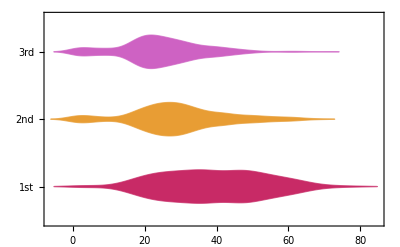
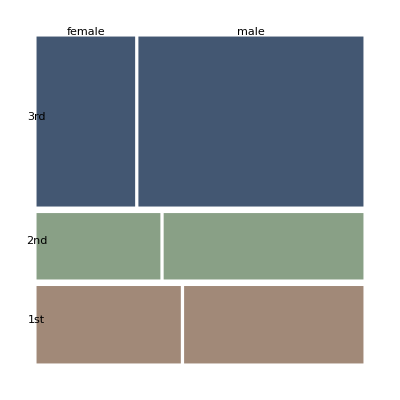
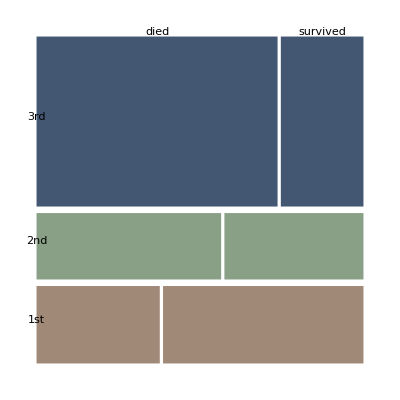
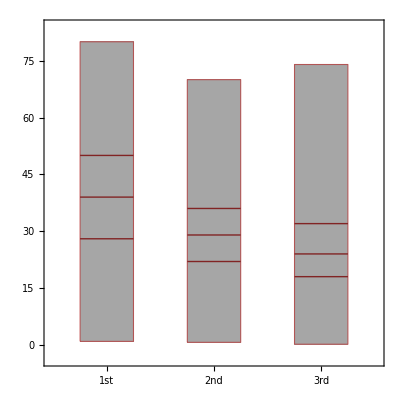
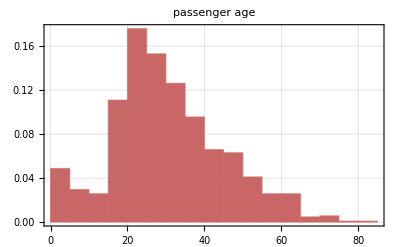
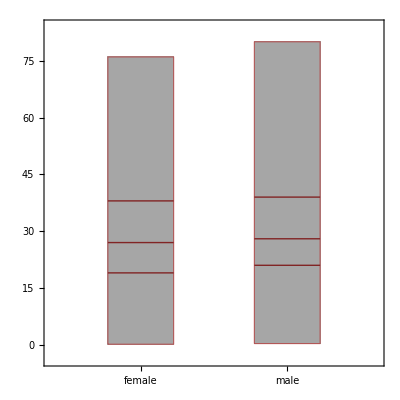
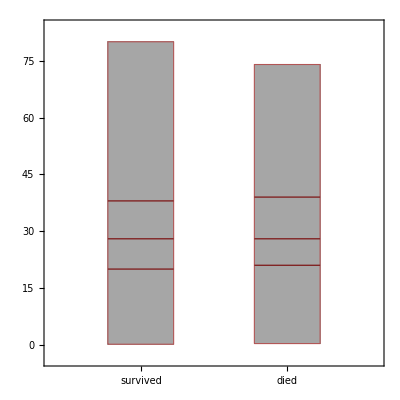
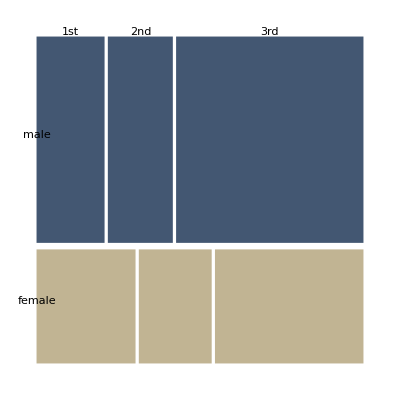
passenger class | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | passenger sex | -Graphics-
-Graphics- | -Graphics- | -Graphics- | passenger survival

```mathematica
Magnify[#, 1.] &@VariableDependenceGrid[titanicData, columnNames]
```

```mathematica
data = ExampleData[{"MachineLearning", "Titanic"}, "TrainingData"];
data = ((Flatten@*List) @@@ data)[[All, {1, 2, 3, -1}]];
trainingData = DeleteCases[data, {___, _Missing, ___}];
Dimensions[trainingData]
```

{732,4}

```mathematica
data = ExampleData[{"MachineLearning", "Titanic"}, "TestData"];
data = ((Flatten@*List) @@@ data)[[All, {1, 2, 3, -1}]];
testData = DeleteCases[data, {___, _Missing, ___}];
Dimensions[testData]
```

{314,4}

```mathematica
trainingData = trainingData /. {"survived" -> 1, "died" -> 0, "1st" -> 0, "2nd" -> 1, "3rd" -> 2, "male" -> 0, "female" -> 1};

testData = testData /. {"survived" -> 1, "died" -> 0, "1st" -> 1, "2nd" -> 2, "3rd" -> 3, "male" -> 0, "female" -> 1};
```

```mathematica
lfm = LinearModelFit[{trainingData[[All, 1 ;; -2]], trainingData[[All, -1]]}]
```

FittedModel[-0.0136025 #1+0.00515243 #2+0.634046 #3]

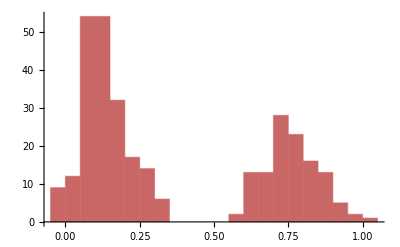

```mathematica
modelValues = lfm @@@ testData[[All, 1 ;; -2]];

Histogram[modelValues, 20]
```

```mathematica
testData[[1]]
```

{1,25.,1,0}

```mathematica
testLabels = testData[[All, -1]];
thRange = Range[0.1, 0.9, 0.025];
aROCs = Table[ToROCAssociation[{0, 1}, testLabels, 
	Map[If[# > θ, 1, 0] &, modelValues]], {θ, thRange}];
```

```mathematica
Through[ROCFunctions[{"PPV", "NPV", "TPR", "ACC", "SPC"}][aROCs[[3]]]]
```

{34/43,19/37,17/32,197/314,95/122}

```mathematica
ROCPlot[thRange, aROCs, 
	"PlotJoined" -> Automatic, 
	"ROCPointCallouts" -> True, 
	"ROCPointTooltips" -> True, 
	GridLines -> Automatic]
```

-Graphics-

```mathematica
thRange
```

{0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9}

```mathematica
FullForm[aROCs[[1]]]
```

Association[Rule["TruePositive",61],Rule["FalsePositive",14],Rule["TrueNegative",108],Rule["FalseNegative",131]]

## Seeking Forecast windows

## Conclusion

The quite revolution of numerical prediction has brought

The quiet revolution of numerical weather models has been boosting a consistent increase in accuracy and extension of weather predictions. The progress require keeping clarifying the boundary between weather and climate.  
Extratropical cyclones, storm tracks.

there is never a sharp distincion

# ENSO

# MJO

# QBO